### Geodesic equation for Schwarzschild metric

From Schwarzschild metric, I had already derived connection coefficients (or Christoffel symbol) corresponds to the metric. Recall that in mind, we can write the geodesic equations with given coefficients.

(x^(..))^μ+(Γ^μ)_(⋁ σ)(ẋ)^v(ẋ)^σ=0  ,  {c t, r, θ , ϕ}

μ=0

t^(..)+(2m)/(r(r-2m))ṫ ṙ=0   ⟹ (1-(2m)/r)ṫ=const=b

μ=2

θ^(..)+2/r ṙ θ̇-sin θ cos θ (ϕ̇)^2=0

μ=3

ϕ^(..)+2/r ṙ ϕ̇+2cot θ θ̇ ϕ̇=0

instead of  μ=1 case, handle  the line element 
 ⅆ s^2=-c^2ⅆ τ^2=-(1-(2m)/r)c^2 ⅆ t^2+(1-(2m)/r)^-1 ⅆ r^2+r^2 ⅆ Ω^2  divide it by  ⅆ s^2=-c^2ⅆ τ^2

1=(1-(2m)/r)(ṫ)^2-(1-(2m)/r)^-1 (ṙ)^2/c^2-r^2/c^2((θ̇)^2+sin^2 θ (ϕ̇)^2) . 
For light, on the other hand,

0=(1-(2m)/r)(ṫ)^2-(1-(2m)/r)^-1 (ṙ)^2/c^2-r^2/c^2((θ̇)^2+sin^2 θ (ϕ̇)^2) .

Now consider a geodesic passing through the equator, θ=π/2, namely  θ̇=0 , then,

μ=0

t^(..)+(2m)/(r(r-2m))ṫ ṙ=0   ⟹ (1-(2m)/r)ṫ=const=b

μ=2

θ^(..)=0

μ=3

ϕ^(..)+2/r ṙ ϕ̇=0 ⟹ (r^2 ϕ̇)=const=a  , ṙ=(ⅆ r)/(ⅆ ϕ)(ⅆ ϕ)/(ⅆ t)=(ⅆ r)/(ⅆ ϕ)ϕ̇=(ⅆ r)/(ⅆ ϕ)a/r^2

Substitute those into geodesic equation.

1=(1-(2m)/r)(ṫ)^2-(1-(2m)/r)^-1 (ṙ)^2/c^2-r^2/c^2((θ̇)^2+sin^2 θ (ϕ̇)^2)   ,(θ=π/2, θ̇=0)

1= (1-(2m)/r)^-1 b^2-(1-(2m)/r)^-1 (a^2/c^2[ⅆ/ⅆϕ(1/r)])^2-a^2/c^2 1/r^2

(1-(2m)/r)1/a^2=b^2/a^2-(1/c^2[ⅆ/ⅆϕ(1/r)])^2-1/(r^2 c^2)(1-(2m)/r)

[ⅆ/ⅆϕ(1/r)]^2+1/r^2=(c^2 b^2)/a^2+((2m)/r-1)c^2/a^2+(2m)/(c^2 r^3) , or

[ⅆ/ⅆϕ(1/r)]^2+1/r^2=(c^2 b^2)/a^2+(2m)/(c^2 r^3) (for light)

differentiate with respect to ϕ

2ⅆ/(ⅆ ϕ)(1/r)ⅆ^2/(ⅆ ϕ^2)(1/r)+2/r ⅆ/ⅆϕ(1/r)=(2m c^2)/a^2 ⅆ/ⅆϕ(1/r)+2m 3(1/r)^2 ⅆ/ⅆϕ(1/r)

assume that  ⅆ/ⅆϕ(1/r) ≠ 0 , (rejecting circle trajectory case) then,

ⅆ^2/(ⅆ ϕ^2)(1/r)+1/r=(m c^2)/a^2+(3m)/r^2  or,

ⅆ^2/(ⅆ ϕ^2)(1/r)+1/r=(3m)/r^2  (light)  where  m=G M/c^2

let G → 1  and c → 1 and see what happens when light travel around the black hole!

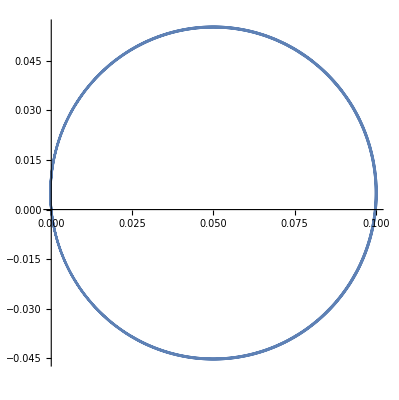

```mathematica
M=0.01;
s=NDSolveValue[{w''[ϕ]+w[ϕ]==3M(w[ϕ])^2,w[0]==0.1,w'[0]==0.01},w,{ϕ,0,4π}];
PolarPlot[s[x],{x,0.,4π},AspectRatio->Automatic]
```

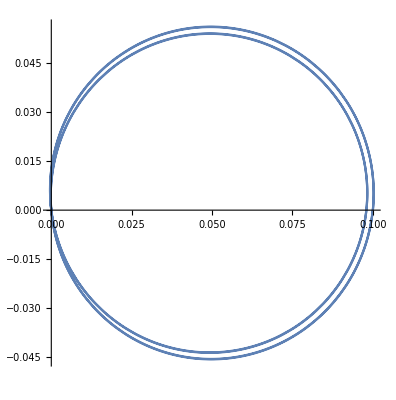

```mathematica
M=0.1;
s=NDSolveValue[{w''[ϕ]+w[ϕ]==3M(w[ϕ])^2,w[0]==0.1,w'[0]==0.01},w,{ϕ,0,4π}];
PolarPlot[s[x],{x,0,4π}]
```

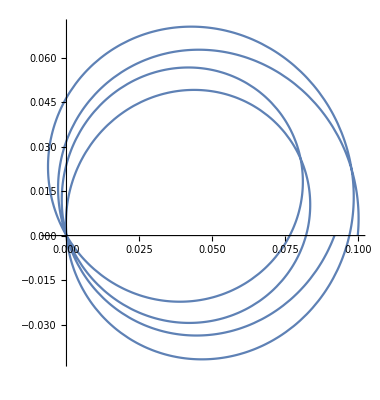

```mathematica
M=0.9;
s=NDSolveValue[{w''[ϕ]+w[ϕ]==3M(w[ϕ])^2,w[0]==0.1,w'[0]==0.01},w,{ϕ,0,4π}];
PolarPlot[s[x],{x,0,4π}]
```

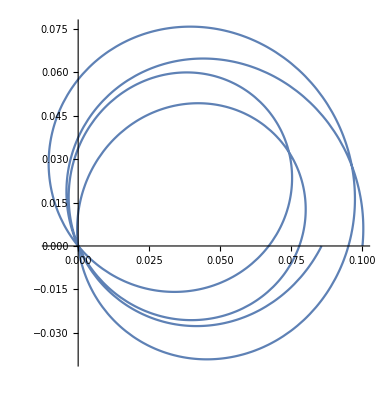

```mathematica
M=1.1;
s=NDSolveValue[{w''[ϕ]+w[ϕ]==3M(w[ϕ])^2,w[0]==0.1,w'[0]==0.01},w,{ϕ,0,4π}];
PolarPlot[s[x],{x,0,4π}]
```

Matter case (1/a^2=2)

```mathematica
M=0.1;
s=NDSolveValue[{w''[ϕ]+w[ϕ]==3M(w[ϕ])^2+2M,w[0]==0.1,w'[0]==0.01},w,{ϕ,0,40π}];
Manipulate[PolarPlot[s[x],{x,0,ϕ}],{ϕ,5π,40π,5π}]
```

We can see the precession!